```mathematica
nbp[n0_]:=n0/(n0+5.5 N[CDF[PoissonDistribution[5.5],n]])
nbn[n0_]:=n0/(n0+5.5 N[(1-CDF[PoissonDistribution[5.5],n])])
pttabp=ParallelTable[N[nbp[10000,n]],{n,1,50,1}];//AbsoluteTiming
pttabn=ParallelTable[N[nbn[10000,n]],{n,1,50,1}];//AbsoluteTiming
```

{0.033075,Null}

{0.0198578,Null}

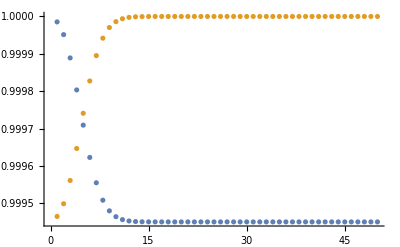

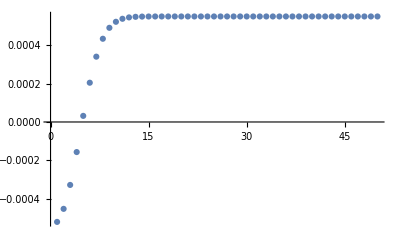

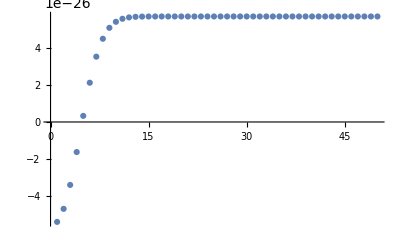

```mathematica
ListPlot[{pttabp,pttabn},PlotRange->Full]
ListPlot[-{pttabp-pttabn},PlotRange->Full]
ListPlot[-{pttabp-pttabn}*1.04*10^(-22),PlotRange->Full]
```

```mathematica
N[Integrate[1000/(1000+5.5 N[CDF[PoissonDistribution[5.5],n]]),{n,0,5.5}]]
```

5.49482